```mathematica
w[t_] = 800/(1+3*Exp[-t/30])
```

800/(1+3 ⅇ^(-t/30))

```mathematica
dwdt = D[w[t],t]
```

(80 ⅇ^(-t/30))/((1+3 ⅇ^(-t/30))^2)

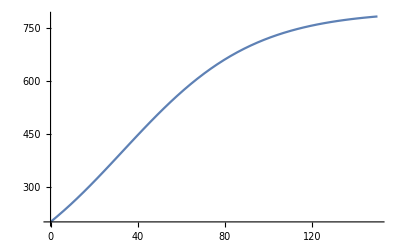

```mathematica
Plot[w[t], {t, 0, 150}]
```

```mathematica
p[t_]=(.65-.01t)*800/(1+3*Exp[-t/30])-.45t
```

(800 (0.65-0.01 t))/(1+3 ⅇ^(-t/30))-0.45 t

```mathematica
(*) Part b
```

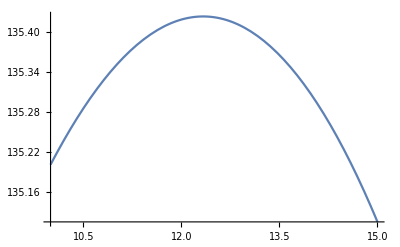

```mathematica
Plot[p[t],{ t, 10, 15}]
```

```mathematica
p'[t]
```

-0.45-8./(1+3 ⅇ^(-t/30))+(80 ⅇ^(-t/30) (0.65-0.01 t))/((1+3 ⅇ^(-t/30))^2)

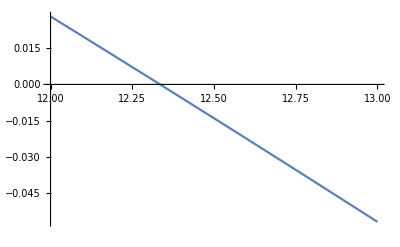

```mathematica
Plot[p'[t], {t, 12,13}]
```

```mathematica
(*)Determining zeroes of p'[t] by Newton's Method
```

```mathematica
tn[t_]=t - p'[t]/D[p'[t],t];
N[NestList[tn, 12.3000000, 20],10]
```

{12.3,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349,12.3349}

```mathematica
p[12.339]
```

135.424

```mathematica
(*)Part c
```

```mathematica
Clear[p]
```

```mathematica
p[t_]=(.65-.01t)*k/(1+3*Exp[-t/30])-.45t
```

(k (0.65-0.01 t))/(1+3 ⅇ^(-t/30))-0.45 t

```mathematica
(.65-.01*12.3349)/(1+3*Exp[-12.3349/30])*800/135.42
```

1.04102

```mathematica
p'[t]
```

-0.45-(0.01 k)/(1+3 ⅇ^(-t/30))+(ⅇ^(-t/30) k (0.65-0.01 t))/(10 (1+3 ⅇ^(-t/30))^2)

```mathematica
k=808
```

808

```mathematica
p[t]
```

(808 (0.65-0.01 t))/(1+3 ⅇ^(-t/30))-0.45 t

```mathematica
p'[t]
```

-0.45-8.08/(1+3 ⅇ^(-t/30))+(404 ⅇ^(-t/30) (0.65-0.01 t))/(5 (1+3 ⅇ^(-t/30))^2)

```mathematica
tn[t_]=t - p'[t]/D[p'[t],t];
N[NestList[tn, 12.3, 20],10]
```

{12.3,12.3879,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877,12.3877}